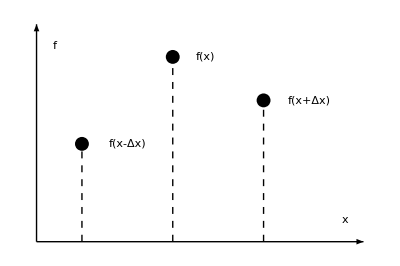

```mathematica
fnfig=Graphics[{
Arrow[{{0,0},{0,1}}],
Arrow[{{0,0},{1.8,0}}],
Dashed,
Line[{{0.25,0},{0.25,0.45}}],
Line[{{0.75,0},{0.75,0.85}}],
Line[{{1.25,0},{1.25,0.65}}],
PointSize[0.025],
Point[{0.25,0.45}],
Point[{0.75,0.85}],
Point[{1.25,0.65}],
FontSize->22,FontFamily->Times,
Text["f",{0.1,0.9}],
Text["x",{1.7,0.1}],
FontSize->18,
Text["f(x-Δx)",{0.5,0.45}],
Text["f(x)",{0.93,0.85}],
Text["f(x+Δx)",{1.5,0.65}]
},ImageSize->{300},AspectRatio->1/1.5
]
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["examfig.pdf",fnfig]
```

C:\Users\James\Box\teaching\P427\assignments\exams

examfig.pdf